```mathematica
(* script1 :generating fusible numbers *)
```

```mathematica
(*generating fusible numbers*)
cond[a_]:=Abs[a[[2]]-a[[1]]]<1
sim[a_,b_]:=(a+b+1)/2
nextFusibles[fusiblesIn_]:=Module[{t,newFusibles},
t=Select[Tuples[fusiblesIn,5],cond];
newFusibles=Table[sim[t[[i,1]],t[[i,2]]],{i,1,Length[t]}];
DeleteDuplicates[Join[fusiblesIn,newFusibles]]
]
```

```mathematica
Nest[nextFusibles,{0},5]
```

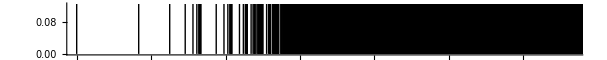

```mathematica
(*this visualizes the denisity of fusible numbers*)
Nest[nextFusibles,{0},10]//Graphics[{Line[{{#,0},{#,1/8}}]&/@#},Axes->{True,False},PlotRange->{{0,4},All},ImageSize->10 72,
AspectRatio->1/10]&
```

```mathematica
ClearAll[fusibleN];
fusibleN[b_]:=1-2^(-1-(b-2));
```

```mathematica
fusibleN[Range[25]]
```

```mathematica
fusibleN[b_]:=1-2^(-1-(b-2));
```

```mathematica
Block[{$RecursionLimit = 10^4}, RepeatedTiming[fusibleN[10^3/2]]]
```

```mathematica
N[Last[%], 155]
```

```mathematica
(* script2 :Ordinals and Transfinite Numbers *)
```

### 2.2. Limit ordinals

```mathematica
fusibleN2[b_]:=5/4-2^(-1-(b+1));
fusibleN2[Range[0,15]]
```

{1,9/8,19/16,39/32,79/64,159/128,319/256,639/512,1279/1024,2559/2048,5119/4096,10239/8192,20479/16384,40959/32768,81919/65536,163839/131072}

Also, for 11/8 (3ω) the fusible numbers between 5/4 and 11/8 have the formula 11/8-1-2^-n for n ∈ N

```mathematica
fusibleN3[b_]:=11/8-2^(-1-(b+1));
fusibleN3[Range[10]]
```

{5/4,21/16,43/32,87/64,175/128,351/256,703/512,1407/1024,2815/2048,5631/4096}

These limit points all converge to 3/2: a 'double limit point ', which we can associate withω^2:

```mathematica
fusibleN4[b_]:=3/2-2^(-(b+1))-2^(-(b+1));
fusibleN4[Range[10]]
```

{1,5/4,11/8,23/16,47/32,95/64,191/128,383/256,767/512,1535/1024}

```mathematica
N[%]
```

{1.,1.25,1.375,1.4375,1.46875,1.48438,1.49219,1.49609,1.49805,1.49902}

```mathematica
(*finding formulae for these following regions turned out to be a challenge*)
```

Continuing to apply the fuse operation in the same manner, we are also applying 3/4∼ and 7/8∼ to the existing fusible numbers; the gaps between successive infinities themselves get very small. We now reach a ‘triple limit point’: 7/4 (ω^3), ‘quadruple’: 15/8 (ω^4), ‘quintuple’: 31/16 (ω^5), ‘sextuple’ limit point: 63/32 (ω^6) and so on until we reach a multitude of limit of limits: 2 (ω^ω), 3 (ω^(ω^(ω^ω))), 4 (ω^(ω^(ω^ω))) and eventually we reach the order type of the fusible numbers: ord(F) = ε₀.

```mathematica
ordinals={1,1.125,1.25,1.5, 1.625,1.75,1.875 ,2, 3};
ordinalLabels={ω,ω+1, ω2, ω^2,2 ω^2,ω^3,ω^4, ω^ω, ω^(ω^ω)};
```

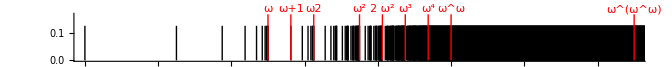

```mathematica
Nest[nextFusibles,{0},10]//Graphics[{Line[{{#,0},{#,1/8}}]&/@#,{Red,Line[{{#,0},{#,1/6}}]&/@ordinals,MapThread[Inset[#2,{#1,1/6},{0,-1.5}]&,{ordinals,ordinalLabels}]}},Axes->{True,False},PlotRange->{{0,3},All},ImageSize->10 72,AspectRatio->1/10]&
```

an updated graphic with some transfinite ordinals

### 2.3. An algorithm that translates a fusible number to its ordinal, vice-versa

#### 2.3.1. Integer fusible numbers

Let’s consider the simplest case: translating integer fusible numbers to their corresponding ordinals. This is a simple task, as Ordinal(x+1)=ω^(Ordinal(x)). Following algorithm, although trivial, nevertheless illustrates the towers of infinite ordinals:

```mathematica
ClearAll[Ordinal]
Ordinal[n_Integer]:=Nest[ω^#1&,1, n]
Manipulate[Ordinal[u],{u,0,100,1}]
```

```mathematica
Ordinal[7]
```

ω^(ω^(ω^(ω^(ω^(ω^ω)))))

this algorithm works for all the fusible numbers until ε₀

#### 2.3.2. From ordinals to fusible numbers

In section 2.2 we used separate formulae for calculating the sequences of fusible numbers; there were discontinuities in these sequences due to accumulation points; this makes the pairing the two representations difficult.

The following function is an example of transitioning between fusible numbers and their corresponding ordinals. It is a low-yielding one, however, as it only finds corresponding fusible numbers between the lowest transfinite ordinal ω and the second ω2, e.g. when inputting ω+299792458, it outputs the corresponding fusible number. Ideally one wants a a more general formulae for calculating the sequences of fusible numbers in different sections along the real line.

```mathematica
fusibleN2[b_]:=5/4-2^(-1-(b+1));
fusibleN2[Range[0,15]];
Table[ω+u,{u,0,10}];
OrdtoFuse[Plus[ω,n_Integer]]:=fusibleN2[n]
```

```mathematica
OrdtoFuse[ω+12098]
```

### 2.4. The recursive algorithm: finding successive fusible numbers

Again, based on the well-ordering principle, Xu et al., on that basis, have defined the following recursive algorithm that allows us to find fusible numbers greater than x .

Theorem Xu et al. [2]. Algorithm M terminates on all real inputs.

M (x) Piecewise[{{-x, if x<0}, {m(x-a-1/d+2^[^log 2^a])/2, otherwise}}]

Through implementation,

```mathematica
m[x_]:=Sow[If[x<0,-x,Module[{y,v=2 x-1,d,e},(y=v-s[x-1];
d=m[y];
y=y+d);
While[(y=p[y];
2 y>v),(y=v-s[v-y];
e=m[y];
d=Min[d,e];
y=y+e)];
d/2]]];
s[x_]:=x+m[x];
```

```mathematica
N[m[2]]
N[s[2]]
```

0.000976563

2.00098

we can compute both m(x): giving us the smallest distance to the next fusible number and s(x): the smallest fusible number over that distance. As highlighted, this recursive algorithm is prone to fail sooner or later given the incredibly fast-growing nature of the fuse operation:

m(0)=0.5, t(0)=0.5; 
m(1)=0.125,  t(1)=1.125; 
m(2)=0.000976563; t(x)=2.00098
m(3)= 2^-1541023937 [3]
m(4)=may be well-greater than Graham's number [1].
m(5)...

One point to add, anything above m(2) took simply too long to calculate: following function shows the recursive calls made by m(x). This implies the inefficiency of m(x). We also considered finding a non-recursive algorithm that would overcome the computational costs associated with it, but were unsuccessful.

recursive calls made by the algorithm m(x) for m(2)

```mathematica
With[
{mValues=Reap[m[2]],
maxXRange=1000},
Manipulate[
ListLinePlot[
Take[mValues[[2,1]],UpTo[xRange]],
PlotLabel->mValues[[1]],
PlotRange->{{0,maxXRange},{0,1}},
AspectRatio->1/5,
GridLines->{None,{mValues[[1]]}},
GridLinesStyle->Directive[Thickness[0.001],Red],
Method->{"GridLinesInFront"->True},
ImageSize->800
],
{xRange,1,maxXRange,1}
]]
```

```mathematica
Reap[m[Rationalize[2]]][[2,1]]//Length
```

40117

### 2.5. Algorithm for deciding whether a given number is fusible

Additionally, one of the tasks of this project was to create an algorithm FusibleQ that decides whether a number is fusible or not.  For starers, an obvious criteria that tests for ‘fusibility’ is to consider only dyadic rationals as potential candidates. Nevertheless, the trouble with finding a general formula, is that, by definition we  have an infinite collection of fusible numbers all of which can go into constructing that particular fusible number that we are testing the ‘fusibility’ on. That property makes these types of computations difficult. The same notion also became an obstacle in the section 3.2 whilst creating an algorithm that deconstructs fusible numbers into its component parts.

### 2.6. Approximating π ,√2 ... from fusible numbers

The following algorithm gives us the list of ‘the closest approximate fusible numbers’ from our data. We were able to find rough approximates to π  and to√2. Overall, we can get infinitely closer to building any arbitrary (irrational) numbers through the ‘fusion’ of more and more numbers, all of which are potentially useful for approximating to any arbitrary number.

```mathematica
cond[a_]:=Abs[a[[2]]-a[[1]]]<1
sim[a_,b_]:=(a+b+1)/2
nextFusibles[fusiblesIn_]:=Module[{t,newFusibles},
t=Select[Tuples[fusiblesIn,2],cond];
newFusibles=Table[sim[t[[i,1]],t[[i,2]]],{i,1,Length[t]}];
DeleteDuplicates[Join[fusiblesIn,newFusibles]]
]
fusibleData[n_]:=Nest[nextFusibles,{0},n];
```

```mathematica
fuseApprox[x_,n_]:=Sort[fusibleData[n],Abs[#1-Pi]<Abs[#2-Sqrt[2]]&]
```

```mathematica
N[First[fuseApprox[Pi,12]]]
```

3.1416

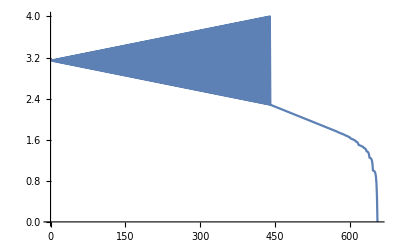

```mathematica
fuseApprox[Pi,8]//ListLinePlot
```

```mathematica
N[First[fuseApprox[Sqrt[2],10]]]
```

2.1416

## 3. Individual fusible numbers

### Subsection 3.1. Representing fusible numbers as binary trees

Part of Erickson et al . 1 Theorem 1.3. ”Every fusible number x∈F has a maximum-height representation h_max(x).”

On the basis of the binary fuse operation, each fusible number can also be represented as a binary tree which itself embeds into a larger tree structure: if T(x_1) embeds into T(x_2) then x_1≤x_2. That simple statement can also be used as a basis for the proof behind the well-ordering of fusible numbers e.g. Kruskal’s tree theorem [2]. Moreover, almost all fusible numbers can be ‘engineered’ differently and can all have differing heights:

-Graphics-

a few random combinations for 43/32, showcasing ‘binary branching’

Nevertheless, every fusible number has a maximum-height representation; otherwise the well-ordering principle would not hold. What follows, are some 'snapshots' of fusible numbers, based on the number of leaves.

```mathematica
fuse[a_,b_]:=(a+b+1)/2
FuseTree[a_,b_]:=FuseTree[a,b]=Tree[fuse[TreeData[a], TreeData[b]],{a,b}]
Groupings[ConstantArray[Tree[0,None],6],FuseTree->{2 ,Orderless}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### 3.2. Deconstructing fusible numbers to its minimal binary tree compositions

Some examples on the basis of which the algorithm was built:

|  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
ClearAll[partitions2]
partitions2[n_Integer?OddQ]:=With[{x=Range[(n-1)/2]},Prepend[Thread[{x,n-x}],{0,n}]]
partitions2[n_Integer?EvenQ]:=With[{x=Range[n/2]},Prepend[Thread[{x,n-x}],{0,n}]]
```

```mathematica
partitions2/@Range[5]//Column
```

{{0,1}}
{{0,2},{1,1}}
{{0,3},{1,2}}
{{0,4},{1,3},{2,2}}
{{0,5},{1,4},{2,3}}

```mathematica
ClearAll[decompose]
decompose[n:(_Integer|_Rational)]/;n>0 :=
Rule@@@descend[n]
descend[n_Rational]/;n>0:=
Module[{k=2n-1,p,q},
If[k<0,Return[{}]];p=partitions2[Numerator[k]]/Denominator[k]//DeleteCases[{i_,j_}/;Abs[i-j]>1];q=MapApply[𝒻,Catenate/@DeleteCases[Map[descend,p,{2}],{{},_}|{_,{}}]];
Map[𝒻[n,MapApply[𝒻,#]]&,q]
]
descend[n_Integer]/;n>0:=
With[{f=descend/@Table[(2n-1)/2,{2}]},
𝒻[n,𝒻@@#]&/@Thread@f
]
descend[0]:={0}
```

```mathematica
decompose[1]
```

{1→𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]}

```mathematica
decompose[2]
```

{2→𝒻[𝒻[3/2,𝒻[𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]],𝒻[3/2,𝒻[𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]]]}

0<n<1

```mathematica
decompose[1/2]
```

{1/2→𝒻[0,0]}

```mathematica
decompose[3/4]
```

{3/4→𝒻[0,𝒻[1/2,𝒻[0,0]]]}

1<n<2

```mathematica
decompose[7/8]
```

{7/8→𝒻[0,𝒻[3/4,𝒻[0,𝒻[1/2,𝒻[0,0]]]]]}

```mathematica
decompose[9/8]
```

{9/8→𝒻[𝒻[1/2,𝒻[0,0]],𝒻[3/4,𝒻[0,𝒻[1/2,𝒻[0,0]]]]]}

```mathematica
decompose[3/2]
```

{3/2→𝒻[𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]}

5/4 should generate two decompositions

```mathematica
{5/4->{1/2,1},5/4->{3/4,3/4}}
```

```mathematica
decompose[5/4]
```

{5/4→𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]}

```mathematica
2(5/4)-1
```

3/2

```mathematica
partitions2[3]/2
```

{{0,3/2},{1/2,1}}

the first pair is rejected as their difference is greater than 1

try 6/4

```mathematica
partitions2[6]/4
```

{{0,3/2},{1/4,5/4},{1/2,1},{3/4,3/4}}

```mathematica
partitions2[12]/8
```

{{0,3/2},{1/8,11/8},{1/4,5/4},{3/8,9/8},{1/2,1},{5/8,7/8},{3/4,3/4}}

the first three are rejected as their differences are greater than 1

```mathematica
decompose[3/8]
```

{}

```mathematica
decompose[5/8]
```

{}

two pairs survive: {1/2,1} and {3/4,3/4}

integers

```mathematica
decompose[0]
```

decompose[0]

```mathematica
decompose[1]
```

{1→𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]}

```mathematica
decompose[2]
```

{2→𝒻[𝒻[3/2,𝒻[𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]],𝒻[3/2,𝒻[𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]]]}

```mathematica
decompose[3]
```

{3→𝒻[𝒻[5/2,𝒻[𝒻[2,𝒻[𝒻[3/2,𝒻[𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]],𝒻[3/2,𝒻[𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]]]],𝒻[2,𝒻[𝒻[3/2,𝒻[𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]],𝒻[3/2,𝒻[𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]]]]]],𝒻[5/2,𝒻[𝒻[2,𝒻[𝒻[3/2,𝒻[𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]],𝒻[3/2,𝒻[𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]]]],𝒻[2,𝒻[𝒻[3/2,𝒻[𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]],𝒻[3/2,𝒻[𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]],𝒻[1,𝒻[𝒻[1/2,𝒻[0,0]],𝒻[1/2,𝒻[0,0]]]]]]]]]]]}

Overall, the algorithm does what it is supposed to do, reducing fusible numbers to their minimal component parts. However, there are some minor issues: 5/4  seems to be a problem; when doing the decomposition, we only find one of the partitions that work, the other partition needs to be tweaked: the rational number needs to be changed from 3/4 to 6/8 in order for the decomposition to work.

## script: combinators 4. Fusible number-combinator connection

Schönfinkel’s combinators can be thought of as symbolic expressions represented as trees. Similarly, as we learned already, we are able to represent the evolution of fusible numbers as trees of differing heights and more formally, we can think of as the leaves of the trees being 0’s and the internal nodes being the fuse operation (∼). Let’s consider some simple examples: 

    -Graphics-

1/2= (0 ∼ 0) and 1=(0 ∼ 0) ∼ (0 ∼ 0)

Moreover, as already showcased, the same fusible numbers can have differing structures. In the zero-tilde notation, 3/4 can be represented either as (0~0)~0 or  0~(0~0)

```mathematica
-Graphics-        -Graphics-
```

```mathematica
an example from Erickson [1],fusible number 5/4:
```

```mathematica
t1="(0~(0~0))~(0~(0~0))";
t2="(0~0)~((0~0)~(0~0))";
```

In using the zero-tilde notation, we’ll try to use S-combinators to generate fusible numbers.

```mathematica
ClearAll[naughtsToTree]
naughtsToTree::usage="naughtsToTree[string] returns a Tree expression for the 0-tilde representation of a fusible number.";
Options[naughtsToTree]=Sort@Join[{},Options[Tree]];
naughtsToTree[naughts_String,opts:OptionsPattern[]]/;StringMatchQ[naughts,("("|")"|"0"|"~")..]:=
ToExpression@If[StringFreeQ[naughts,"~"],naughts,StringReplace["("<>naughts<>")",{"("->"{",")"->"}","~"->","}]]//fn//ExpressionTree[#,FilterRules[{opts},Options[Tree]],ImageSize->(18+36(Count[#,0,{0,∞}]-1))]&
fn[0]:=0
fn[pair:{_,_}]:=Module[{a,b},{a,b}=fn/@pair;(((Plus@@Head/@{a,b}/.Integer->0)+1)/2)[a,b]]
```

```mathematica
treeToCombinator::usage="treeToCombinator[t] returns an  combinator expression for the fusible number Tree expression t.";
treeToCombinator[t_Tree]:=With[{c=Replace[TreeChildren[t],None->{}]},Switch[c,{},,{_,_},treeToCombinator[First@c][treeToCombinator[Last@c]],_,Echo[c];$Failed]]
```

```mathematica
ClearAll[combinatorToTree,combinatorToTreeRecurse]
combinatorToTree::usage="combinatorToTree[c] returns the fusible number Tree expression for the \!\(\*TemplateBox[{},\n\"CombinatorS\"]\) combinator c.";
combinatorToTree[c_]:=Catch@combinatorToTreeRecurse[c]
combinatorToTreeRecurse[CombinatorS]:=Tree[0,None,ImageSize->18]
combinatorToTreeRecurse[l_[r_]]:=combinatorToTreeRecurse[l[r]]=Module[{lFn=combinatorToTreeRecurse[l],rFn=combinatorToTreeRecurse[r],a,b},a=TreeData[lFn];
b=TreeData[rFn];
If[Abs[a-b]>=1,Throw[Tree[$Failed,None,ImageSize->54]]];
Tree[(a+b+1)/2,Replace[#,{Tree[0,None]->0,t_:>Tree[TreeData[t],TreeChildren[t]]}]&/@{lFn,rFn},ImageSize->18+36 (Total[(ImageSize-18)/36+1/. Options/@{lFn,rFn}]-1)]]
```

```mathematica
naughtsToTree["0"]
```

-Graphics-

```mathematica
treeToCombinator@%
```

```mathematica
combinatorToTree@%
```

-Graphics-

```mathematica
naughtsToTree["0~0"]
```

-Graphics-

```mathematica
treeToCombinator@%
```

[]

```mathematica
combinatorToTree@%
```

-Graphics-

```mathematica
naughtsToTree["0~(0~0)"]
```

-Graphics-

```mathematica
treeToCombinator@%
```

[[]]

```mathematica
combinatorToTree@%
```

-Graphics-

```mathematica
naughtsToTree["(0~0)~0"]
```

-Graphics-

```mathematica
treeToCombinator@%
```

[][]

```mathematica
combinatorToTree@%
```

-Graphics-

```mathematica
naughtsToTree[t1]
```

-Graphics-

```mathematica
treeToCombinator@%
```

[[]][[[]]]

```mathematica
combinatorToTree@%
```

-Graphics-

```mathematica
naughtsToTree[t2]
```

-Graphics-

```mathematica
treeToCombinator@%
```

[][[][[]]]

```mathematica
combinatorToTree@%
```

-Graphics-

```mathematica
naughtsToTree["0~(0~(0~(0~(0~0))))"]
```

-Graphics-

```mathematica
treeToCombinator@%
```

[[[[[]]]]]

```mathematica
combinatorToTree@%
```

-Graphics-

```mathematica
naughtsToTree["((((0~0)~0)~0)~0)~0"]
```

-Graphics-

```mathematica
treeToCombinator@%
```

[][][][][]

```mathematica
combinatorToTree@%
```

-Graphics-

## 5. Plotting all the ‘fusion’ events

### Subsection 5.1. The token-event graph

Now we generate all the possible combinations of fusible numbers in the confines of a reasonable number of time-steps. First, we have plotted the results onto a simple nested graph that has tokens in the middle. These tokens act as disambiguation by showing how the precursor numbers are fed in pairs to create the new numbers through the fuse operation; whereas the actual nodes of the graph are the fusible numbers themselves. Therefore, our nested graph was split into two classes:

```mathematica
fuseCombine[a_,b_]:=If[Abs[b-a]<1,(a+b+1)/2,Nothing]
With[{
data=Nest[Function[{levelSets},
Append[levelSets,Complement[
Union[Catenate@Outer[Function[{comb},
If[SameQ[comb,Nothing],Nothing,
 Sort[{#1,#2}]->comb
]][fuseCombine[#1,#2]]&,
Last/@Flatten[levelSets],
Last/@Last[levelSets],1]],
Flatten[levelSets]]
]][#]&,{{{0,0}->0}},6]},
g=VertexDelete[Graph[Union[Flatten[data],
Flatten[{#[[1]]->#,#[[2]]->#
}&/@Flatten[data][[All,1]]]],
VertexSize->0.6,
AspectRatio->1/2,
VertexShapeFunction->"RoundedDiamond",
VertexStyle->{x_List:>Red,x_/;NumberQ[x]:>Blue},
GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->{Opacity[0.75],_->Directive[Thin]},
VertexLabels->None],
{0,0}]]
```

the first few ‘fusion’ events

continuing for longer we get a more complex structure:

The result is a widening DAG-graph, showing the possible ‘fusion’ events; how the fusible numbers are created and related to each other. The total number of distinct numbers reached is relatively high, but for a more thorough analysis more time-steps need to be performed.

```mathematica
DirectedGraphQ[%]
```

True

```mathematica
AcyclicGraphQ[%]
```

True

```mathematica
LoopFreeGraphQ[%]
```

True

The graph that follows, has been run for more time steps and has had events removed; only showcasing all the possible fusible numbers generated.

```mathematica
ClearAll[TokenGraph]
TokenGraph[g_Graph,opts:OptionsPattern[Graph]]:=Module[{InEdges,OutEdges,edges,vertices},InEdges=Cases[EdgeList[g],_->{_,_}]//GroupBy[#,Last->First]&//KeySort;
OutEdges=Cases[EdgeList[g],{_,_}->_]//GroupBy[#,First->Last]&//KeySort;
edges=Catenate@MapThread[Catenate@Outer[DirectedEdge,##]&,{InEdges,OutEdges}];
vertices=Cases[VertexList[g],Except[{_,_}]];
Graph[vertices,edges,opts,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->None,
EdgeStyle->{Opacity[.75],_->Directive[Thin]}]
]
```

```mathematica
t=ReverseGraph[TokenGraph[g,AspectRatio->1/2]]
```

-Graphics-

A token-graph showing the behaviour of fusible numbers; here the 0, from where ‘fusing’ begins, is at the bottom.